```mathematica
(***  Mathematica notebook with the modules for the DGIG distribution  (PDF and CDF), modules DGIGpdf and DGIGcdf  ***)
```

```mathematica
Rat[x_]:=Module[{nn},
If [ToString[Head[x]]≠"Real",x,
nn=StringLength[ToString[x,InputForm]]-1;Round[x*10^nn]/10^nn]]

SetAttributes[Rat,Listable]

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Table[c=ReplacePart[c,(Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}])/(r[[i]]-1)!,{i,r[[i]]}],{i,1,p}];
Table[Table[c=ReplacePart[c,Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{i,r[[i]]-k}],{k,1,r[[i]]-1}],{i,1,p}];
c
]

P[c_,d_,r1_,r2_,l1_,l2_,z_]:=Table[Sum[c[[j]][[k]]*Sum[Sum[d[[ell]][[h]]*Sum[Binomial[k-1,i]*z^(k-1-i)*(h+i-1)!/(l1[[j]]+l2[[ell]])^(h+i),{i,0,k-1}],{h,1,r2[[ell]]}],{ell,1,Length[r2]}],{k,1,r1[[j]]}],{j,1,Length[r1]}];

(* Computation for z=0 *)

P0[c_,d_,r1_,r2_,l1_,l2_,z_]:=Table[Sum[c[[j]][[k]]*Sum[Sum[d[[ell]][[h]]*(h+k-2)!/(l1[[j]]+l2[[ell]])^(h+k-1),{h,1,r2[[ell]]}],{ell,1,Length[r2]}],{k,1,r1[[j]]}],{j,1,Length[r1]}];

DGIGpdf[r1_,r2_,li1_,li2_,zi_,prec_:50]:=Module[{p1,p2,l1,l2,c,d,PP,K1,K2,z},If[Count[r1,_Integer]==Length[r1]&&Count[r2,_Integer]==Length[r2]&&And@@Positive[r1]&& And@@Positive[r2]&&And@@Positive[li1]&&And@@Positive[li2]&&Length[r1]==Length[li1]&&Length[r2]==Length[li2],
p1=Length[r1];
p2=Length[r2];
l1=Rat[li1];
l2=Rat[li2];
z=Rat[zi];
c=Makec[r1,l1,p1];
d=Makec[r2,l2,p2];
PP=If[z>0,P[c,d,r1,r2,l1,l2,z],If[z==0,P0[c,d,r1,r2,l1,l2,z],P[d,c,r2,r1,l2,l1,-z]]];
K1=Product[l1[[j]]^r1[[j]],{j,1,p1}];
K2=Product[l2[[j]]^r2[[j]],{j,1,p2}];
SetPrecision[If[z>0,K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],If[z==0,K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],K1*K2*Sum[PP[[ell]]*Exp[l2[[ell]]*z],{ell,1,p2}]]],50]
]
]

DGIGpdf::usage="DGIGpdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG pdf. It has 6 arguments (the first 5 are mandatory): r1 - list of the shape parameters for the Gamma distributions with positive sign; r2 - list of the shape parameters for the Gamma distributions with negative sign; l1 - list of the rate parameters for the Gamma distributions with positive sign; l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the PDF has to be computed; prec - number of precision digits to be used in the computation (default value 50)";

PS[c_,d_,r1_,r2_,l1_,l2_,z_]:=Table[Sum[c[[j]][[k]]*Sum[Sum[d[[ell]][[h]]*Sum[Binomial[k-1,i]*(h+i-1)!/(l1[[j]]+l2[[ell]])^(h+i)*Sum[(k-1-i)!/t!*If[z==0&&t==0,1,z^t]/l1[[j]]^(k-i-t),{t,0,k-1-i}],{i,0,k-1}],{h,1,r2[[ell]]}],{ell,1,Length[r2]}],{k,1,r1[[j]]}],{j,1,Length[r1]}];

DGIGcdf[r1_,r2_,li1_,li2_,zi_,prec_:50]:=Module[{p1,p2,l1,l2,c,d,PP,K1,K2,z},
If[Count[r1,_Integer]==Length[r1]&&Count[r2,_Integer]==Length[r2]&&And@@Positive[r1]&& And@@Positive[r2]&&And@@Positive[li1]&&And@@Positive[li2]&&Length[r1]==Length[li1]&&Length[r2]==Length[li2],
p1=Length[r1];
p2=Length[r2];
l1=Rat[li1];
l2=Rat[li2];
z=Rat[zi];
c=Makec[r1,l1,p1];
d=Makec[r2,l2,p2];
PP=If[z≥0,PS[c,d,r1,r2,l1,l2,z],PS[d,c,r2,r1,l2,l1,-z]];
K1=Product[l1[[j]]^r1[[j]],{j,1,p1}];
K2=Product[l2[[j]]^r2[[j]],{j,1,p2}];
SetPrecision[If[z≥0,1-K1*K2*Sum[PP[[j]]*Exp[-l1[[j]]*z],{j,1,p1}],K1*K2*Sum[PP[[ell]]*Exp[l2[[ell]]*z],{ell,1,p2}]],prec]
]
]

DGIGcdf::usage="DGIGcdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG cdf. It has 6 arguments (the first 5 are mandatory): r1 - list of the shape parameters for the Gamma distributions with positive sign; r2 - list of the shape parameters for the Gamma distributions with negative sign; l1 - list of the rate parameters for the Gamma distributions with positive sign; l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the CDF has to be computed; prec - number of precision digits to be used in the computation (default value 50)";
```

```mathematica
?DGIGpdf
```

DGIGpdf[r1, r2, l1, l2, z, prec_:50] computes the DGIG pdf. It has 6 arguments (the first 5 are mandatory): r1 - list of the shape parameters for the Gamma distributions with positive sign; r2 - list of the shape parameters for the Gamma distributions with negative sign; l1 - list of the rate parameters for the Gamma distributions with positive sign; l2 - list of the rate parameters for the Gamma distributions with negative sign; z - running value where the PDF has to be computed; prec - number of precision digits to be used in the computation (default value 50)

0.3641322847859112009417299452939550278391227612121

0.8416816153104733908949000237852369444177727125165

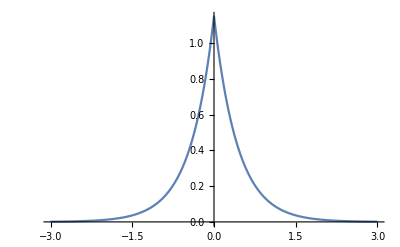

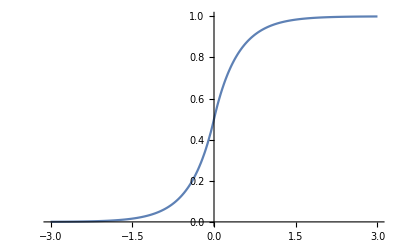

```mathematica
r1={1};m1={23/10};r2=r1;m2=m1;
z=.5;
DGIGpdf[r1,r2,m1,m2,z]
DGIGcdf[r1,r2,m1,m2,z]
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-3,3}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-3,3}]
```

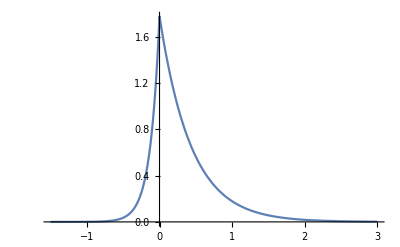

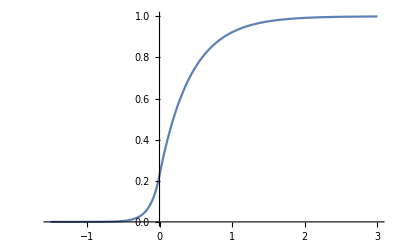

```mathematica
r1={1};m1={23/10};r2=r1;m2={78/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-1.5,3},PlotRange->All]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-1.5,3}]
```

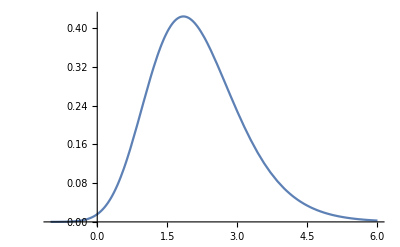

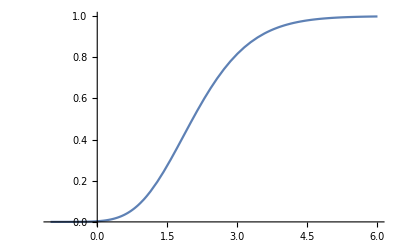

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};r2={6,7};m2={123/10,154/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-1,6}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-1,6}]
```

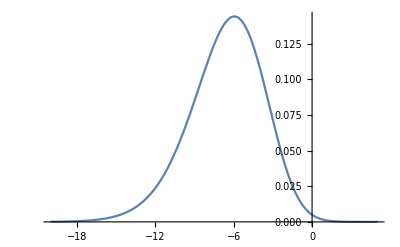

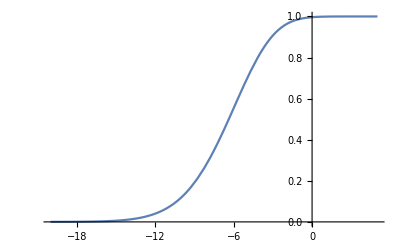

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};r2={6,7};m2={12/10,15/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-20,5}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-20,5}]
```

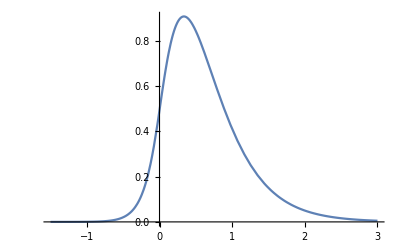

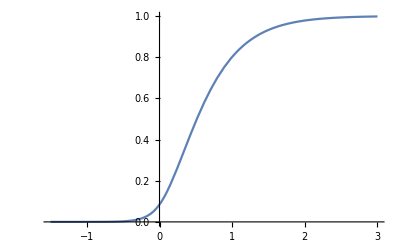

```mathematica
r1={1,1,1};m1={23/10,44/10,56/10};r2={1,1};m2={78/10,98/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-1.5,3},PlotRange->All]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-1.5,3}]
```

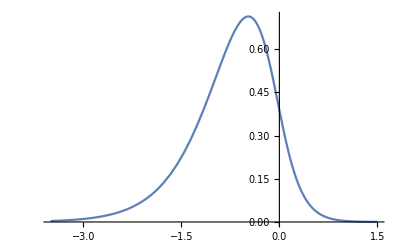

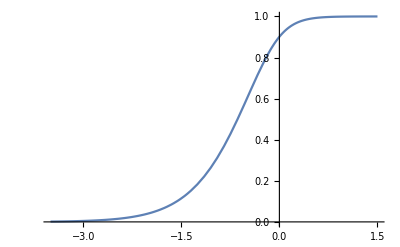

```mathematica
r1={1,1,1};m1={78/10,98/10,56/10};r2={1,1,1,1};m2={23/10,44/10,56/10,34/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-3.5,1.5},PlotRange->All]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-3.5,1.5}]
```

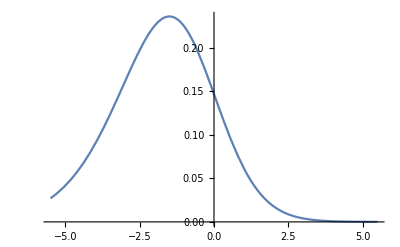

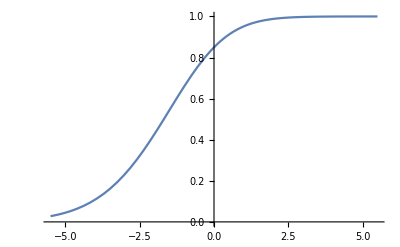

```mathematica
r1={3,4,5};
m1={23/10,45/10,56/10};
m2={67/10,15/10,37/10,54/10};
r2={2,4,5,3};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

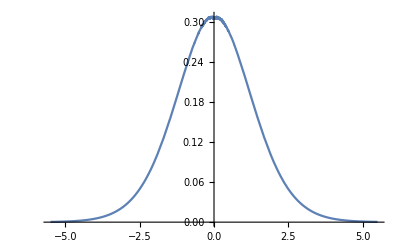

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};r2=r1;m2=m1;
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5},PlotRange->All]
```

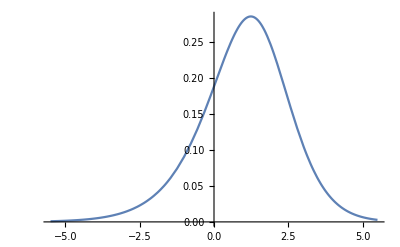

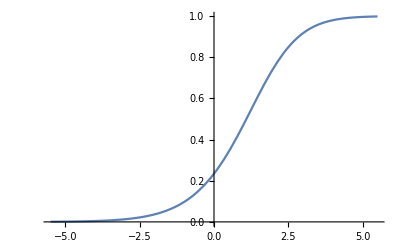

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
Plot[DGIGcdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

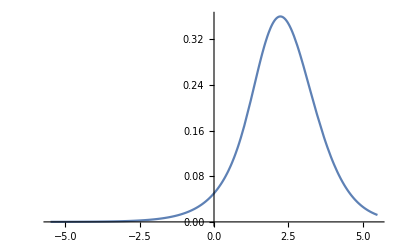

```mathematica
r1={3,4,5};m1={23/10,45/10,56/10};
r2={1};m2={12/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

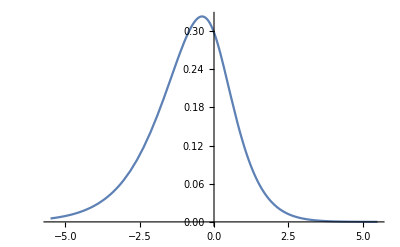

```mathematica
r1={3};m1={23/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,5.5}]
```

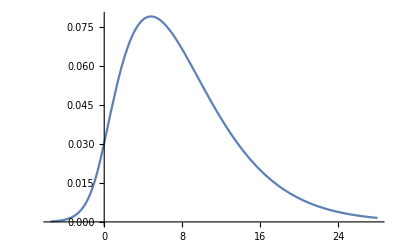

```mathematica
r1={3};m1={3/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,28}]
```

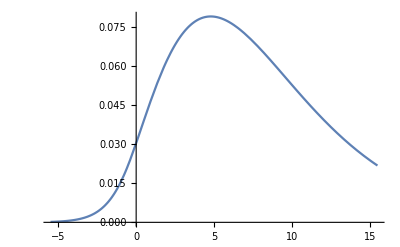

```mathematica
r1={3};m1={3/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,15.5},PlotRange->All]
```

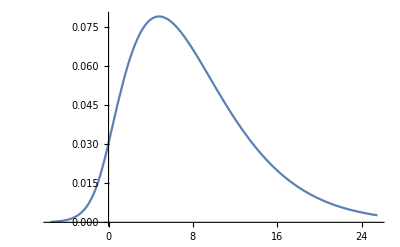

```mathematica
r1={3};m1={3/10};
r2={1,1,1};m2={12/10,15/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-5.5,25.5},PlotRange->All]
```

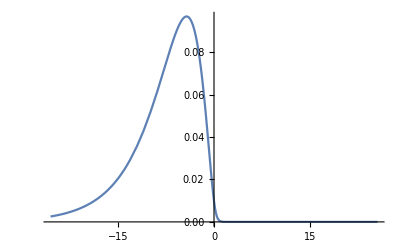

```mathematica
r1={3};m1={53/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25.5,25.5}]
```

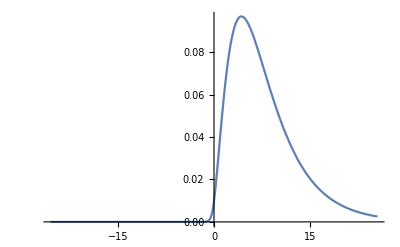

```mathematica
r1={3};m1={53/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r2,r1,m2,m1,x],{x,-25.5,25.5}]
```

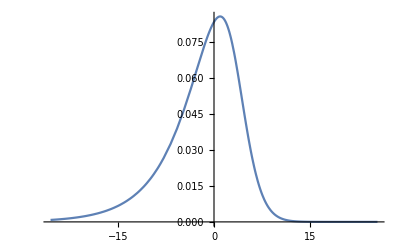

```mathematica
r1={3,5,7};m1={53/10,74/10,26/20};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25.5,25.5}]
```

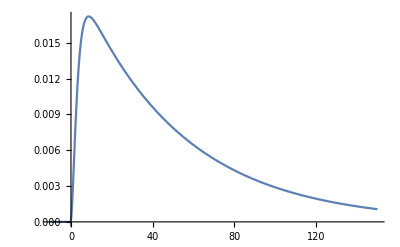

```mathematica
r1={3};m1={153/10};
r2={1,1,1};m2={2/100,5/10,7/10};
Plot[DGIGpdf[r2,r1,m2,m1,x],{x,-10,150}]
```

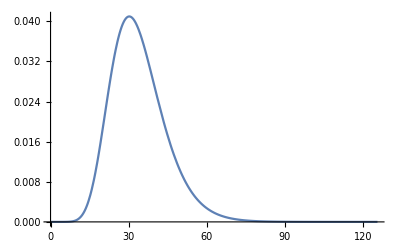

```mathematica
r1={3,5,7};m2={53/10,74/10,26/20};
r2={1,1,1};m1={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,0,125.5}]
```

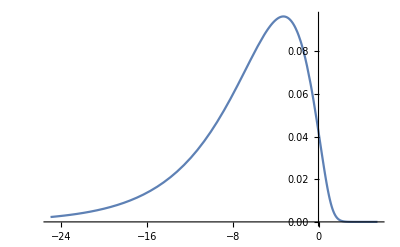

```mathematica
r1={3,5,7};m1={153/10,174/10,126/20};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25,5.5}]
```

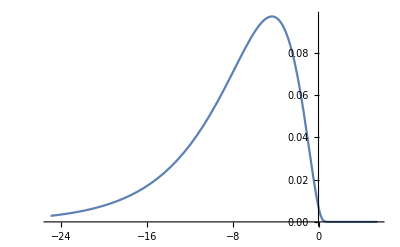

```mathematica
r1={3,5};m1={153/10,174/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25,5.5}]
```

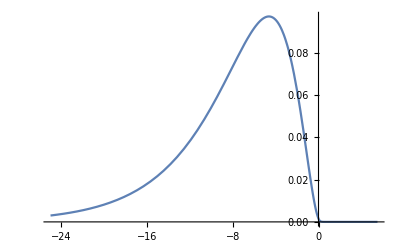

```mathematica
r1={3};m1={153/10};
r2={1,1,1};m2={2/10,5/10,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-25,5.5}]
```

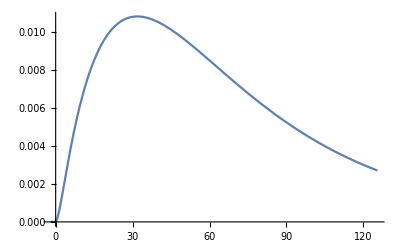

```mathematica
r2={3};m2={153/10};
r1={1,1,1};m1={2/100,5/100,7/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-2,125.5}]
```

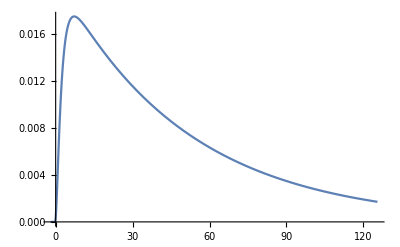

```mathematica
r2={3};m2={153/10};
r1={1,1,1};m1={2/100,5/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-2,125.5}]
```

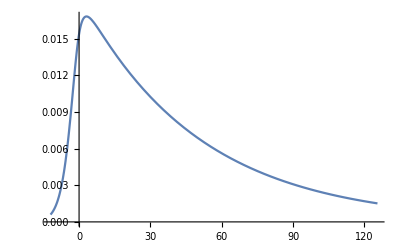

```mathematica
r2={3,3};m2={153/10,5/10};
r1={1,1,1};m1={2/100,5/10,17/10};
Plot[DGIGpdf[r1,r2,m1,m2,x],{x,-12,125.5}]
```

```mathematica
r1={2,3,4};
r2={5,6};
l1=Rat[{1.2,2.3,3.4}];
l2=Rat[{7.8,8.9}];
c=Makec[r1,l1,3];
d=Makec[r2,l2,2];
SetPrecision[P[c,d,r1,r2,l1,l2,Rat[3.4]],30]
DGIGpdf[r1,r2,l1,l2,-3.4]
```

{2.1287624139969174098299659651×10^-15,1.61642611062261795795006554418×10^-11,-2.46877412692002437432120284129×10^-11}

4.822752160579111682238385643327066376644004837×10^-9

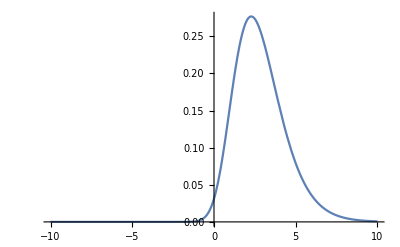

```mathematica
Plot[DGIGpdf[r1,r2,l1,l2,x],{x,-10,10}]
```